This notebook imports dat files, and plots energy eigenvalues and LDoS of projected QAHI

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
datFileLDOSlocation="/HOTI/LDOS/";
datfileOBCName="t0=1.0_t=1.0_m_0=-1.0_Delta=1.0_x_periodic=0_y_periodic=0_L=60_m=0.6666666666666666_c1=7_c2=13";
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[dataLDoSOBC,colorfunc]
```

```mathematica
(** Change the filenames accordingly and import the dat files **)
```

```mathematica
dataLDoSOBCdat=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLDOSlocation,datfileOBCName,".csv"]]];
```

```mathematica
largestX = Dimensions[dataLDoSOBCdat][[1]];
```

```mathematica
dataLDoSOBC=Table[{nn,0,dataLDoSOBCdat[[nn]]},{nn,1,largestX}];
```

```mathematica
colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];
```

```mathematica
Clear[Lattice];
```

```mathematica
Lattice=Table[{j,0},{j,1,largestX}];
```

```mathematica
Dimensions[dataLDoSOBCdat]
```

{380}

```mathematica
largestX
```

380

```mathematica
rngOld={0,Max[#]}&@dataLDoSOBC[[All,3]]
```

{0,0.538651}

```mathematica
rng={0,0.54}
```

{0,0.54}

```mathematica
P1=BarLegend[{colorfunc[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 15},Ticks-> {{0,"0.0"},{rng[[2]]/2,"0.27"},{rng[[2]]-10^-3,"0.54"}}]
```

```mathematica
(** Crop the image appropriately and put the numbers in inkscape **)
```

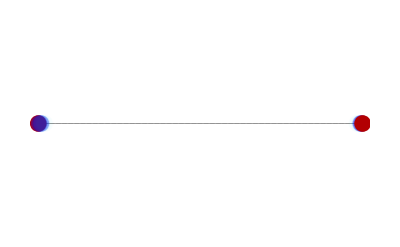

```mathematica
plt2=Show[
ListPlot[Lattice,Frame-> False,Axes-> False,PlotStyle-> {Black,PointSize[0.001]},PlotRange-> {All,{-2,2}}],
Graphics[{Opacity[0.1],
PointSize[0.03],colorfunc[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@dataLDoSOBC,
BaseStyle-> 18
]

]
```

```mathematica
Export[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLDOSlocation,datfileOBCName,"_linear.pdf"],plt2];
Export[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLDOSlocation,datfileOBCName,"_linear_colorbar.pdf"],P1];
```